# AntonAntonov/ClassifierEnsembles

Creation of- and classification with ensembles of classifiers

## Paclet Manifest

"Documentation"

"English"

"Guides"

"Ensemblesofclassifiers.nb"DocumentationEnglishGuidesEnsemblesofclassifiers.nb

"ReferencePages"

"Symbols"

"ClassifyByThreshold.nb"DocumentationEnglishReferencePagesSymbolsClassifyByThreshold.nb

"EnsembleClassifierConfusionMatrix.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierConfusionMatrix.nb

"EnsembleClassifierMeasurements.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierMeasurements.nb

"EnsembleClassifier.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifier.nb

"EnsembleClassifierProbabilities.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierProbabilities.nb

"EnsembleClassifierROCData.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierROCData.nb

"EnsembleClassifierROCPlots.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierROCPlots.nb

"EnsembleClassifierVotes.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifierVotes.nb

"EnsembleClassifyByThreshold.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassifyByThreshold.nb

"EnsembleClassify.nb"DocumentationEnglishReferencePagesSymbolsEnsembleClassify.nb

"ResamplingEnsembleClassifier.nb"DocumentationEnglishReferencePagesSymbolsResamplingEnsembleClassifier.nb

"Tutorials"

"Kernel"

"ClassifierEnsembles.wl"KernelClassifierEnsembles.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image



### Basic Description

Functions of creating Machine Learning classifier ensembles and making classifications using votes, averaged probabilities, and thresholds.

### Details

A classifier ensemble is created with a list of names of the algorithms used by Classify.

Using Automatic all (relevant) classifier making algorithms for the given data are used.

A given record is classified by default using the average probabilities for the labels given by the classfiers.

Also, a given record can be classfied by using the number of classifier votes for the labels.

Thresholds for the individual labels can be specified.

### Primary Context

AntonAntonov`ClassifierEnsembles`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`ClassifierEnsembles`"];
```

### Basic Examples

Get training data:

```mathematica
data=ExampleData[{"MachineLearning","Titanic"},"TrainingData"];
data=((Flatten@*List)@@@data)[[All,{1,2,3,-1}]];
trainingData=DeleteCases[data,{___,_Missing,___}];
```

Get testing data:

```mathematica
data=ExampleData[{"MachineLearning","Titanic"},"TestData"];
data=((Flatten@*List)@@@data)[[All,{1,2,3,-1}]];
testData=DeleteCases[data,{___,_Missing,___}];
```

```mathematica
ResourceFunction["RecordsSummary"][trainingData]
```

{1 column 1
3rd | 354
1st | 197
2nd | 181,2 column 2
Min | 0.3333
1st Qu | 21.
Median | 27.
Mean | 29.4164
3rd Qu | 38.
Max | 80.,3 column 3
male | 460
female | 272,4 column 4
died | 427
survived | 305}

Create a classifier ensemble using Classify method names:

```mathematica
aCLs=EnsembleClassifier[{"LogisticRegression","NearestNeighbors","RandomForest","GradientBoostedTrees","NaiveBayes"},trainingData[[All,1;;-2]]->trainingData[[All,-1]]];
aCLs//Rasterize
```

-Graphics-

#### Classify a record

Classify a record with the ensemble:

```mathematica
EnsembleClassify[aCLs,testData[[1,1;;-2]]]
```

survived

Classify a record using classifier votes and specifying 2 to be the threshold for the label "survived":

```mathematica
EnsembleClassifyByThreshold[aCLs,testData[[1,1;;-2]],"survived"->2,"Votes"]
```

survived

Classify a record using the mean of the probabilities given by each classifier and a threshold for "survived":

```mathematica
EnsembleClassifyByThreshold[aCLs,testData[[1,1;;-2]],"survived"->0.2,"ProbabilitiesMean"]
```

survived

#### Classify a list of records using a threshold

Classify a list of records and return "survived" if it gets at least two votes:

```mathematica
EnsembleClassifyByThreshold[aCLs,testData[[1;;12,1;;-2]],"survived"->2,"Votes"]
```

{survived,died,survived,died,died,survived,died,survived,died,survived,died,survived}

Return "survived" if its average probability is at least 0.7:

```mathematica
EnsembleClassifyByThreshold[aCLs,testData[[1;;12,1;;-2]],"survived"->0.7,"ProbabilitiesMean"]
```

{survived,died,survived,died,died,survived,died,survived,died,survived,died,survived}

#### Threshold classification with ROC

Compute Receiver Operating Characteristic (ROC) for a range of thresholds for the label "survived":

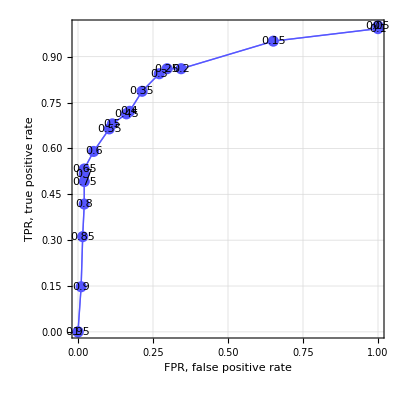

```mathematica
Needs["AntonAntonov`ROCFunctions`"];
rocRange=Range[0,1,0.05];
aROCs=Table[(cres=EnsembleClassifyByThreshold[aCLs,testData[[All,1;;-2]],"survived"->i];
ToROCAssociation[{"survived","died"},testData[[All,-1]],cres]),{i,rocRange}];
ROCPlot[rocRange,aROCs,GridLines->Automatic]
```

### Scope

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-ClassifierEnsembles-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Classification

Classifier

Ensemble

Classifier ensemble

ROC functions

Machine Learning

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

AntonAntonov/DataReshapers

AntonAntonov/ROCFunctions

### Original Source References and Attributions

ROC for classifier ensembles, bootstrapping, damaging, and interpolation | Mathematica for prediction algorithms

### Links

MathematicaForPrediction/ClassifierEnsembles.m at master · antononcube/MathematicaForPrediction · GitHub

### Compatibility

#### Wolfram Language Version

12.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.